## Profile Generation

### Sigmoidal Function

```mathematica
c[z_]:=1/(1+Exp[-z])
```

### Interpolating Dielectric Profile - Dimensionless Grouped

```mathematica
qSubs=Collect[q->r c[s]+c[a]-(r+1)c[-a],r,Simplify]
```

q→(-1+ⅇ^a)/(1+ⅇ^a)+(-1/(1+ⅇ^a)+1/(1+ⅇ^-s)) r

```mathematica
odeXsDG=0==Collect[(Ex''[s]+(q Ω^2)/(c[a]-c[-a])Ex[s])/.qSubs,{Ex[s],Ex''[s]},Simplify]
```

0==((-1+ⅇ^a-ⅇ^s-r+ⅇ^(a+s) (1+r)) Ω^2 Ex[s])/((-1+ⅇ^a) (1+ⅇ^s))+Ex''[s]

```mathematica
JoinedScalesSubs={r->δ^α,a->δ^β,s->ξ δ^β,Ω->δ^γ,Ex[s]->Ex[ξ],Ex''[s]->δ^(-2β)  Ex''[ξ]}
```

{r→δ^α,a→δ^β,s→δ^β ξ,Ω→δ^γ,Ex[s]→Ex[ξ],Ex''[s]→δ^(-2 β) Ex''[ξ]}

```mathematica
odeXξJS=Collect[Expand[δ^(2β)odeXsDG[[2]]/.JoinedScalesSubs],{Ex[ξ],Ex''[ξ]},Simplify]
```

(δ^(2 (β+γ)) (-1+ⅇ^(δ^β)-ⅇ^(δ^β ξ)-δ^α+ⅇ^(δ^β (1+ξ)) (1+δ^α)) Ex[ξ])/((-1+ⅇ^(δ^β)) (1+ⅇ^(δ^β ξ)))+Ex''[ξ]

## Thick Layer Approximation

```mathematica
Qgeneral=Coefficient[odeXsDG[[2]],Ex[s]]
```

((-1+ⅇ^a-ⅇ^s-r+ⅇ^(a+s) (1+r)) Ω^2)/((-1+ⅇ^a) (1+ⅇ^s))

```mathematica
QaLarge=Limit[Qgeneral/Ω^2,a->Infinity]
```

(1+ⅇ^s (1+r))/(1+ⅇ^s)

```mathematica
PhaseThick=Sqrt[QaLarge]
```

√((1+ⅇ^s (1+r))/(1+ⅇ^s))

```mathematica
Limit[PhaseThick,s->-Infinity]
```

1

```mathematica
Limit[PhaseThick,s->Infinity]
```

√(1+r)

```mathematica
Solve[0==D[QaLarge,s,s,s]//Simplify,s]
```

{{s→ConditionalExpression[2 ⅈ π C[1]+Log[2-√3],C[1]∈Integers]},{s→ConditionalExpression[2 ⅈ π C[1]+Log[2+√3],C[1]∈Integers]}}

```mathematica
PhaseIntegralThick=Integrate[PhaseThick,s]//Simplify
```

(√(1+ⅇ^s) √((1+ⅇ^s (1+r))/(1+ⅇ^s)) (s-Log[2+ⅇ^s (2+r)+2 √(1+ⅇ^s) √(1+ⅇ^s (1+r))]+√(1+r) Log[2+r+2 ⅇ^s (1+r)+2 √(1+ⅇ^s) √(1+r) √(1+ⅇ^s (1+r))]))/(√(1+ⅇ^s (1+r)))

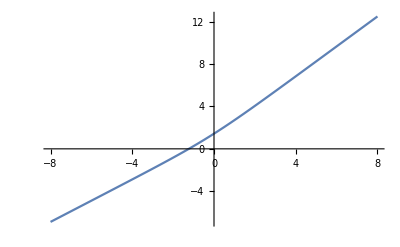

```mathematica
Plot[PhaseIntegralThick/.Table[r->k,{k,1,5}],{s,-8,8}]
```

```mathematica
PhaseIntegralThick/.Table[r->k,{k,1,5}]
```

(√(1+ⅇ^s) √((1+2 ⅇ^s)/(1+ⅇ^s)) (s-Log[2+3 ⅇ^s+2 √(1+ⅇ^s) √(1+2 ⅇ^s)]+√2 Log[3+4 ⅇ^s+2 √2 √(1+ⅇ^s) √(1+2 ⅇ^s)]))/(√(1+2 ⅇ^s))